## 1.0 intro

```mathematica
Clear[H,Hs]
H=RandomVariate[NormalDistribution[],{6,6}];
MatrixForm[H]
Eigenvalues[H]

Hs=(H+Transpose[H])/2;
MatrixForm[Hs]
Eigenvalues[Hs]
```

(0.116971 | -1.00938 | -0.460445 | -0.648554 | -0.279209 | 0.805004
-1.27886 | 1.29483 | 0.289786 | -0.7103 | -0.634491 | 0.215866
-1.10051 | -1.33792 | -0.324435 | -0.25535 | -0.893412 | -0.505374
1.14786 | 0.968773 | -1.11693 | -0.831789 | 0.939036 | -0.0300643
0.0634135 | 0.447728 | 0.615986 | -1.1057 | 1.1296 | 0.232138
1.11879 | 0.942648 | 0.682628 | 1.07657 | 0.751377 | 0.26319)

{1.7444+0. ⅈ,0.505801+0.857755 ⅈ,0.505801-0.857755 ⅈ,-0.420849+0.25378 ⅈ,-0.420849-0.25378 ⅈ,-0.265942+0. ⅈ}

(0.116971 | -1.14412 | -0.780477 | 0.249653 | -0.107898 | 0.961898
-1.14412 | 1.29483 | -0.524068 | 0.129237 | -0.0933818 | 0.579257
-0.780477 | -0.524068 | -0.324435 | -0.686138 | -0.138713 | 0.0886271
0.249653 | 0.129237 | -0.686138 | -0.831789 | -0.0833303 | 0.523255
-0.107898 | -0.0933818 | -0.138713 | -0.0833303 | 1.1296 | 0.491758
0.961898 | 0.579257 | 0.0886271 | 0.523255 | 0.491758 | 0.26319)

{-2.02114,1.99428,1.64009,1.07123,-1.03916,0.00305268}

## Figure 1.1

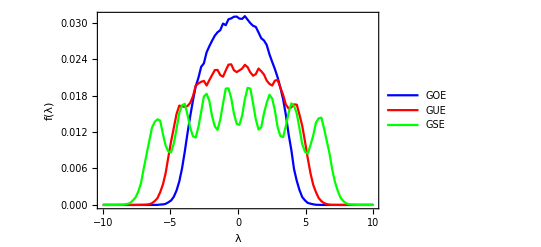

1.81189

1.33343

2.12138

```mathematica
Clear[Ν,H,Hs,T,getGOE,getGUE,getGSE,eigGOE,eigGUE,eigGSE,histGOE,histGUE,histGSE,λdim,λlst]

(* Gaussian Orthogonal Ensemble *)
getGOE[Ν_]:=Module[{H,Hs},
H=RandomVariate[NormalDistribution[],{Ν,Ν}];
Hs=(H+ConjugateTranspose[H])/2;
Return[Eigenvalues[Hs]]
]

(* Gaussian Unitary Ensemble *)
getGUE[Ν_]:=Module[{H,Hs,Has,M},
M=RandomVariate[NormalDistribution[],{Ν,Ν}]+I RandomVariate[NormalDistribution[],{Ν,Ν}];
Hs=(M+ConjugateTranspose[M])/2;
Return[Eigenvalues[Hs]]
]

(* Gaussian Symplectic Ensemble *)
getGSE[Ν_]:=Module[{H,X,Y,A},
X=RandomVariate[NormalDistribution[],{Ν,Ν}]+I RandomVariate[NormalDistribution[],{Ν,Ν}];
Y=RandomVariate[NormalDistribution[],{Ν,Ν}]+I RandomVariate[NormalDistribution[],{Ν,Ν}];
A=ArrayFlatten[{{X,Y},{-Conjugate[Y],Conjugate[X]}}];
H=(A+ConjugateTranspose[A])/2;
Return[DeleteDuplicates[Eigenvalues[H]]]
]

Ν=8;
T=50000;(*50000;*)
λdim=100;(*120*)
λlst=Table[x,{x,-10,+10,20/(λdim-1)}];
eigGOE=Flatten[Table[getGOE[Ν],{i,1,T}]];
eigGUE=Flatten[Table[getGUE[Ν],{i,1,T}]];
eigGSE=Flatten[Table[getGSE[Ν],{i,1,T}]];

histGOE=Transpose[{λlst,BinCounts[eigGOE,{-10,+10,20/λdim}]/(Ν T)}];
histGUE=Transpose[{λlst,BinCounts[eigGUE,{-10,+10,20/λdim}]/(Ν T)}];
histGSE=Transpose[{λlst,BinCounts[eigGSE,{-10,+10,20/λdim}]/(2Ν T)}];
ListPlot[{histGOE,histGUE,histGSE},Joined->True,Frame->True,FrameLabel->{"λ","f(λ)"},PlotStyle->{Blue,Red,Green},PlotLegends->{"GOE","GUE","GSE"}]

Sqrt[Variance[eigGSE]/Variance[eigGOE]]
Sqrt[Variance[eigGUE]/Variance[eigGOE]]
Variance[eigGOE]^0.5
```

## Question 1.3 jpdf of the N(N-1)/2 entries of symmetric matrix Hs

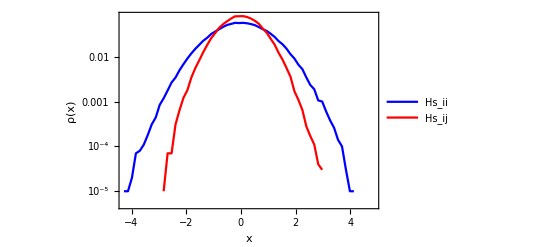

2.01735

```mathematica
Clear[Ν,H,Hs,T,getGOE,getGUE,eigGOE,eigGUE,histGOE,histGUE,λdim,λlst,xii,xij,μii,σii,μij,σij]

(* real symmetric matrix *)
getHs[Ν_]:=Module[{H,Hs},
H=RandomVariate[NormalDistribution[],{Ν,Ν}];
Hs=(H+Transpose[H])/2;
Return[Hs]
]
T=100000;
tabii=Table[getHs[2][[1,1]],{i,1,T}];
tabij=Table[getHs[2][[1,2]],{i,1,T}];

λdim=70;
λlst=Table[x//N,{x,-5,+5,10/(λdim-1)}];
xii=BinCounts[tabii//N,{-5,+5,10/λdim}]/(T);
histii=Transpose[{λlst,xii}];
xij=BinCounts[tabij//N,{-5,+5,10/λdim}]/(T);
histij=Transpose[{λlst,xij}];
ListLogPlot[{histii,histij},Joined->True,Frame->True,FrameLabel->{"x","ρ(x)"},PlotStyle->{Blue,Red},PlotLegends->{"Hs_ii","Hs_ij"}]

(* average and spread for diagonal entries *)
μii=Total[λlst xii]/Total[ xii];
σii=Sqrt[Total[(λlst-μii)^2 xii]/Total[ xii]];

(* average and spread for off-diagonal entries *)
μij=Total[λlst xij]/Total[ xij];
σij=Sqrt[Total[(λlst-μij)^2 xij]/Total[ xij]];

(* ratio of variances *)
(σii/σij)^2
```